```mathematica
PartitionToRealNullSymbol[part_]:=Block[{end},
end=StringRiffle[Map[SetToString[#]&,Sort[part,Min[#1]<Min[#2]&]],"x"];
Symbol["n"<>end]]
```

```mathematica
GenerateRealNullEquations[assoc_]:=Block[
{keysWithoutEdges=Select[Keys[assoc],EdgeCount[assoc[#,"graph"]]==0&]},
Table[PartitionToRealNullSymbol[assoc[key,"vertexsets"]]==assoc[key,"colofour"],{key,keysWithoutEdges}]
]
```

```mathematica
eqsRealNull=GenerateRealNullEquations[allGraphs];
```

```mathematica
repRealNullBase=Map[#[[1]]->#[[2]]&,AndToTable[Reduce[GenerateRealNullEquations[allGraphs],Table[allGraphs[k,"colofour"],{k,atomKeys}]]]];
```

```mathematica
Take[repRealNullBase,2]
```

{v1x2x3x4x5→24 n12345-6 n1234x5-6 n1235x4-2 n123x45+2 n123x4x5-6 n1245x3-2 n124x35+2 n124x3x5-2 n125x34+2 n125x3x4-2 n12x345+n12x34x5+n12x35x4+n12x3x45-n12x3x4x5-6 n1345x2-2 n134x25+2 n134x2x5-2 n135x24+2 n135x2x4-2 n13x245+n13x24x5+n13x25x4+n13x2x45-n13x2x4x5-2 n145x23+2 n145x2x3-2 n14x235+n14x23x5+n14x25x3+n14x2x35-n14x2x3x5-2 n15x234+n15x23x4+n15x24x3+n15x2x34-n15x2x3x4-6 n1x2345+2 n1x234x5+2 n1x235x4+n1x23x45-n1x23x4x5+2 n1x245x3+n1x24x35-n1x24x3x5+n1x25x34-n1x25x3x4+2 n1x2x345-n1x2x34x5-n1x2x35x4-n1x2x3x45+n1x2x3x4x5,v1x2x3x45→-6 n12345+2 n123x45+2 n1245x3+n12x345-n12x3x45+2 n1345x2+n13x245-n13x2x45+n145x23-n145x2x3+2 n1x2345-n1x23x45-n1x245x3-n1x2x345+n1x2x3x45}

```mathematica
Monitor[Table[allGraphs[k,"colofourrealnull"]=Simplify[allGraphs[k,"colofour"]/.repRealNullBase],{k,Keys[allGraphs]}],k];
```

```mathematica
realyNullAtomKeys=Sort[Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofourrealnull"]]]==1&]];Length[realyNullAtomKeys]
```

52

```mathematica
realyNullAtomVars=Table[allGraphs[k,"colofourrealnull"],{k,realyNullAtomKeys}]
```

{n1x2x3x4x5,n1x2x3x45,n1x2x35x4,n1x2x34x5,n1x2x345,n1x25x3x4,n1x25x34,n1x24x3x5,n1x24x35,n1x245x3,n1x23x4x5,n1x23x45,n1x235x4,n1x234x5,n1x2345,n15x2x3x4,n15x2x34,n15x24x3,n15x23x4,n15x234,n14x2x3x5,n14x2x35,n14x25x3,n14x23x5,n14x235,n145x2x3,n145x23,n13x2x4x5,n13x2x45,n13x25x4,n13x24x5,n13x245,n135x2x4,n135x24,n134x2x5,n134x25,n1345x2,n12x3x4x5,n12x3x45,n12x35x4,n12x34x5,n12x345,n125x3x4,n125x34,n124x3x5,n124x35,n1245x3,n123x4x5,n123x45,n1235x4,n1234x5,n12345}

```mathematica
repcolofourrealnullgraph2=Table[allGraphs[k,"colofourrealnull"]->Framed[Labeled[allGraphs[k,"graph"],{Style[allGraphs[k,"colofourrealnull"],Bold],Style[k,ColourForKey[allGraphs,k]]},{Top,Bottom}],FrameStyle->Directive[Red,Dotted,Thick]],{k,realyNullAtomKeys}];
```

```mathematica
repcolofourrealnullgraphsmall=Table[allGraphs[k,"colofourrealnull"]->Framed[Labeled[Graph[allGraphs[k,"graph"],ImageSize->{30,30},VertexLabelStyle->Directive[6]],{Style[allGraphs[k,"colofourrealnull"],Bold,8],Style[k,ColourForKey[allGraphs,k],8]},{Top,Bottom},Spacings->{0,0}],FrameStyle->Directive[Red,Dotted]],{k,realyNullAtomKeys}];Take[repcolofourrealnullgraphsmall,3]
```

{n1x2x3x4x5→-Graphics-n1x2x3x4x50,n1x2x3x45→-Graphics-n1x2x3x452,n1x2x35x4→-Graphics-n1x2x35x46}

```mathematica
CoeffRealNull[exp_]:=Table[Coefficient[exp,var],{var,Sort[realyNullAtomVars]}]
```

```mathematica
Table[allGraphs[k,"graph"]->CoeffRealNull[allGraphs[k,"colofourrealnull"]]/.repcolofourrealnullgraph2,{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]//TableForm
```

-Graphics-→{2,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
-Graphics-→{2,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,-1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
-Graphics-→{2,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,1,0,0,0,0,0,0,0,0}
-Graphics-→{2,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,-1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
-Graphics-→{2,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
CoeffRealNull[allGraphs[k5Key,"colofourrealnull"]]
```

{24,-6,-6,-2,2,-6,-2,2,-2,2,-2,1,1,1,-1,-6,-2,2,-2,2,-2,1,1,1,-1,-2,2,-2,1,1,1,-1,-2,1,1,1,-1,-6,2,2,1,-1,2,1,-1,1,-1,2,-1,-1,-1,1}

```mathematica
(Table[allGraphs[k,"colofourrealnull"],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]//Total)/.repcolofourrealnullgraph2
```

10 -Graphics-n1234559048--Graphics-n1234x557528--Graphics-n1235x454492--Graphics-n1245x345416-2 -Graphics-n124x3543908--Graphics-n1345x218980--Graphics-n1x2345728-2 -Graphics-n14x2354920-2 -Graphics-n135x2414748-2 -Graphics-n13x24513340-2 -Graphics-n134x2517568+-Graphics-n13x24x513284+-Graphics-n13x25x413176+-Graphics-n14x25x34428+-Graphics-n14x2x354380+-Graphics-n1x24x35168

```mathematica
(Table[allGraphs[k,"colofourrealnull"],{k,{quad1Key,quad2Key,quad3Key,quad4Key,quad5Key}}]//Total)/.repcolofourrealnullgraph2
```

-30 -Graphics-n1234559048+6 -Graphics-n1234x557528+6 -Graphics-n1235x454492+-Graphics-n123x4552976+6 -Graphics-n1245x345416+-Graphics-n125x3440896+-Graphics-n12x34539392+4 -Graphics-n124x3543908+6 -Graphics-n1345x218980+-Graphics-n145x236320+-Graphics-n15x2342124+6 -Graphics-n1x2345728+4 -Graphics-n14x2354920+4 -Graphics-n135x2414748+4 -Graphics-n13x24513340+4 -Graphics-n134x2517568--Graphics-n123x4x552974-2 -Graphics-n124x3x543902--Graphics-n125x3x440878--Graphics-n12x35x439372-2 -Graphics-n134x2x517514--Graphics-n14x23x54860--Graphics-n1x234x5666-2 -Graphics-n13x24x513284-2 -Graphics-n135x2x414586-2 -Graphics-n1x235x4546-2 -Graphics-n13x25x413176--Graphics-n13x2x4513124--Graphics-n145x2x35834--Graphics-n15x24x31620-2 -Graphics-n1x245x3218-2 -Graphics-n14x25x34428--Graphics-n1x25x3472--Graphics-n1x2x34526-2 -Graphics-n14x2x354380-2 -Graphics-n1x24x35168+-Graphics-n13x2x4x513122+-Graphics-n14x2x3x54374+-Graphics-n1x24x3x5162+-Graphics-n1x25x3x454+-Graphics-n1x2x35x46

```mathematica
allGraphs[quad1Key,"colofourrealnull"]
```

-6 n12345+2 n1234x5+2 n1235x4+n123x45-n123x4x5+2 n1345x2+n134x25-n134x2x5+n135x24-n135x2x4+2 n13x245-n13x24x5-n13x25x4-n13x2x45+n13x2x4x5

```mathematica
allGraphs[lambdaKey,"colofourrealnull"]
```

4 n12345-n1234x5-n1235x4-n123x45+n123x4x5-n1245x3-n125x34+n125x3x4-n12x345+n12x34x5+n12x3x45-n12x3x4x5-n1345x2-n145x23+n145x2x3-n15x234+n15x23x4+n15x2x34-n15x2x3x4-n1x2345+n1x234x5+n1x23x45-n1x23x4x5+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5

```mathematica
reallyNull=Select[Keys[allGraphs],EdgeCount[allGraphs[#,"graph"]]==0&];
```

```mathematica
Table[Labeled[allGraphs[k,"graph"],Style[k,ColourForKey[allGraphs,k]]],{k,reallyNull}]
```

{-Graphics-0,-Graphics-39366,-Graphics-52974,-Graphics-57528,-Graphics-59048,-Graphics-54492,-Graphics-52976,-Graphics-43902,-Graphics-45416,-Graphics-43908,-Graphics-40878,-Graphics-40896,-Graphics-39384,-Graphics-39392,-Graphics-39372,-Graphics-39368,-Graphics-13122,-Graphics-17514,-Graphics-18980,-Graphics-17568,-Graphics-14586,-Graphics-14748,-Graphics-13284,-Graphics-13340,-Graphics-13176,-Graphics-13124,-Graphics-4374,-Graphics-5834,-Graphics-6320,-Graphics-4860,-Graphics-4920,-Graphics-4428,-Graphics-4380,-Graphics-1458,-Graphics-1944,-Graphics-2124,-Graphics-1620,-Graphics-1476,-Graphics-486,-Graphics-666,-Graphics-728,-Graphics-546,-Graphics-488,-Graphics-162,-Graphics-218,-Graphics-168,-Graphics-54,-Graphics-72,-Graphics-18,-Graphics-26,-Graphics-6,-Graphics-2}

```mathematica
Table[Labeled[allGraphs[k,"colofourrealnull"],Style[k,ColourForKey[allGraphs,k]]],{k,reallyNull}]
```

{n1x2x3x4x50,n12x3x4x539366,n123x4x552974,n1234x557528,n1234559048,n1235x454492,n123x4552976,n124x3x543902,n1245x345416,n124x3543908,n125x3x440878,n125x3440896,n12x34x539384,n12x34539392,n12x35x439372,n12x3x4539368,n13x2x4x513122,n134x2x517514,n1345x218980,n134x2517568,n135x2x414586,n135x2414748,n13x24x513284,n13x24513340,n13x25x413176,n13x2x4513124,n14x2x3x54374,n145x2x35834,n145x236320,n14x23x54860,n14x2354920,n14x25x34428,n14x2x354380,n15x2x3x41458,n15x23x41944,n15x2342124,n15x24x31620,n15x2x341476,n1x23x4x5486,n1x234x5666,n1x2345728,n1x235x4546,n1x23x45488,n1x24x3x5162,n1x245x3218,n1x24x35168,n1x25x3x454,n1x25x3472,n1x2x34x518,n1x2x34526,n1x2x35x46,n1x2x3x452}

## Inequalities de

```mathematica
ineqsrealnull=Table[allGraphs[k,"comp"][allGraphs[k,"colofourrealnull"],0],{k,Keys[allGraphs]}];
```

```mathematica
baserealZero=Table[allGraphs[k,"colofourrealnull"]==0,{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}];
```

```mathematica
realnullAtomFacts=Table[allGraphs[k]["comp"][allGraphs[k]["colofourrealnull"],0],{k,realyNullAtomKeys}];Length[realnullAtomFacts]
```

52

```mathematica
ineqsreal=Table[allGraphs[k,"comp"][allGraphs[k,"colofourrealnull"],0],{k,Keys[allGraphs]}];Length[ineqsreal]
```

1895

```mathematica
countDone=0;MyLeafCount[exp_]:=Block[{},countDone++;StringLength[ToString[exp]]]
```

```mathematica
ineqsnullSimp=Monitor[Simplify[Fold[And,ineqsrealnull],Trig->False,ComplexityFunction->MyLeafCount,Assumptions->realnullAtomFacts],countDone];Length[ineqsnullSimp]
```

1843

```mathematica
allGraphs[2124,"colofournull"]//Expand//Length
```

10

```mathematica
allGraphs[59048,"colofournull"]-allGraphs[2124,"colofournull"]//Expand//Length
```

51

```mathematica
allGraphs[59048,"colofournull"]//Expand//Length
```

52

```mathematica
Select[ineqs,Length[ListofVars[#]]==2&]
```

{v1x2x3x45+v1x2x3x4x5≥0,v1x2x35x4+v1x2x3x4x5≥0,v1x2x345+v1x2x34x5>0,v1x2x34x5+v1x2x3x4x5≥0,v1x2x345+v1x2x35x4>0,v1x2x345+v1x2x3x45>0,v1x25x34+v1x25x3x4≥0,v1x25x3x4+v1x2x3x4x5≥0,v1x25x34+v1x2x34x5>0,v1x24x35+v1x24x3x5≥0,v1x245x3+v1x24x3x5≥0,v1x24x3x5+v1x2x3x4x5≥0,v1x24x35+v1x2x35x4≥0,v1x245x3+v1x25x3x4≥0,v1x245x3+v1x2x3x45>0,v1x23x45+v1x23x4x5>0,v1x235x4+v1x23x4x5>0,v1x2345+v1x234x5>0,v1x234x5+v1x23x4x5>0,v1x2345+v1x235x4>0,v1x2345+v1x23x45>0,v1x23x4x5+v1x2x3x4x5≥0,v1x23x45+v1x2x3x45>0,v1x235x4+v1x25x3x4≥0,v1x235x4+v1x2x35x4≥0,v1x234x5+v1x24x3x5>0,v1x2345+v1x245x3>0,v1x2345+v1x24x35>0,v1x234x5+v1x2x34x5>0,v1x2345+v1x25x34>0,v1x2345+v1x2x345>0,v15x2x34+v15x2x3x4>0,v15x24x3+v15x2x3x4>0,v15x234+v15x23x4>0,v15x23x4+v15x2x3x4>0,v15x234+v15x24x3>0,v15x234+v15x2x34>0,v15x2x3x4+v1x2x3x4x5≥0,v15x2x34+v1x2x34x5>0,v15x24x3+v1x24x3x5≥0,v15x23x4+v1x23x4x5>0,v15x234+v1x234x5>0,v14x2x35+v14x2x3x5≥0,v14x25x3+v14x2x3x5≥0,v14x235+v14x23x5>0,v14x23x5+v14x2x3x5≥0,v14x235+v14x25x3≥0,v14x235+v14x2x35≥0,v145x23+v145x2x3>0,v145x2x3+v14x2x3x5>0,v145x23+v14x23x5>0,v14x2x3x5+v1x2x3x4x5≥0,v14x2x35+v1x2x35x4≥0,v14x25x3+v1x25x3x4≥0,v14x23x5+v1x23x4x5>0,v14x235+v1x235x4>0,v145x2x3+v15x2x3x4>0,v145x23+v15x23x4>0,v145x2x3+v1x2x3x45>0,v145x23+v1x23x45>0,v13x2x45+v13x2x4x5≥0,v13x25x4+v13x2x4x5≥0,v13x245+v13x24x5≥0,v13x24x5+v13x2x4x5≥0,v13x245+v13x25x4≥0,v13x245+v13x2x45>0,v135x24+v135x2x4>0,v135x2x4+v13x2x4x5≥0,v135x24+v13x24x5≥0,v134x25+v134x2x5>0,v1345x2+v134x2x5>0,v134x2x5+v13x2x4x5≥0,v134x25+v13x25x4≥0,v1345x2+v135x2x4>0,v1345x2+v13x2x45>0,v13x2x4x5+v1x2x3x4x5≥0,v13x2x45+v1x2x3x45>0,v13x25x4+v1x25x3x4≥0,v13x24x5+v1x24x3x5≥0,v13x245+v1x245x3>0,v135x2x4+v15x2x3x4>0,v135x24+v15x24x3>0,v135x2x4+v1x2x35x4≥0,v135x24+v1x24x35≥0,v134x2x5+v14x2x3x5≥0,v134x25+v14x25x3≥0,v1345x2+v145x2x3>0,v1345x2+v14x2x35>0,v134x2x5+v1x2x34x5>0,v134x25+v1x25x34>0,v1345x2+v15x2x34>0,v1345x2+v1x2x345>0,v12x3x45+v12x3x4x5>0,v12x35x4+v12x3x4x5>0,v12x345+v12x34x5>0,v12x34x5+v12x3x4x5>0,v12x345+v12x35x4>0,v12x345+v12x3x45>0,v125x34+v125x3x4>0,v125x3x4+v12x3x4x5>0,v125x34+v12x34x5>0,v124x35+v124x3x5>0,v1245x3+v124x3x5>0,v124x3x5+v12x3x4x5>0,v124x35+v12x35x4>0,v1245x3+v125x3x4>0,v1245x3+v12x3x45>0,v123x45+v123x4x5>0,v1235x4+v123x4x5>0,v12345+v1234x5>0,v1234x5+v123x4x5>0,v12345+v1235x4>0,v12345+v123x45>0,v123x4x5+v12x3x4x5>0,v123x45+v12x3x45>0,v1235x4+v125x3x4>0,v1235x4+v12x35x4>0,v1234x5+v124x3x5>0,v12345+v1245x3>0,v12345+v124x35>0,v1234x5+v12x34x5>0,v12345+v125x34>0,v12345+v12x345>0,v12x3x4x5+v1x2x3x4x5≥0,v12x3x45+v1x2x3x45>0,v12x35x4+v1x2x35x4≥0,v12x34x5+v1x2x34x5>0,v12x345+v1x2x345>0,v125x3x4+v15x2x3x4>0,v125x34+v15x2x34>0,v125x3x4+v1x25x3x4>0,v125x34+v1x25x34>0,v124x3x5+v14x2x3x5≥0,v124x35+v14x2x35≥0,v1245x3+v145x2x3>0,v1245x3+v14x25x3>0,v124x3x5+v1x24x3x5≥0,v124x35+v1x24x35≥0,v1245x3+v15x24x3>0,v1245x3+v1x245x3>0,v123x4x5+v13x2x4x5>0,v123x45+v13x2x45>0,v1235x4+v135x2x4>0,v1235x4+v13x25x4>0,v1234x5+v134x2x5>0,v12345+v1345x2>0,v12345+v134x25>0,v1234x5+v13x24x5>0,v12345+v135x24>0,v12345+v13x245>0,v123x4x5+v1x23x4x5>0,v123x45+v1x23x45>0,v1235x4+v15x23x4>0,v1235x4+v1x235x4>0,v1234x5+v14x23x5>0,v12345+v145x23>0,v12345+v14x235>0,v1234x5+v1x234x5>0,v12345+v15x234>0,v12345+v1x2345>0}

```mathematica
Length[Select[ineqs,Length[ListofVars[#]]==2&]]
```

160

```mathematica
Select[ineqsnullSimp,Length[ListofVars[#]]==2&]
```

n1x2x3x4x5>n12x3x4x5&&n1x2345>n12345&&n15x234>n12345&&n1x234x5>n1234x5&&n14x235≥n12345&&n145x23>n12345&&n14x23x5>n1234x5&&n1x235x4>n1235x4&&n15x23x4>n1235x4&&n1x23x4x5>n123x4x5&&n1x23x45>n123x45&&n13x2x4x5>n123x4x5&&n13x245≥n12345&&n135x24≥n12345&&n13x24x5≥n1234x5&&n134x2x5>n1234x5&&n134x25≥n12345&&n1345x2>n12345&&n13x25x4≥n1235x4&&n135x2x4>n1235x4&&n13x2x45>n123x45&&n1x245x3>n1245x3&&n15x24x3>n1245x3&&n1x24x3x5>n124x3x5&&n1x24x35>n124x35&&n14x2x3x5>n124x3x5&&n14x25x3≥n1245x3&&n145x2x3>n1245x3&&n14x2x35>n124x35&&n1x25x3x4>n125x3x4&&n1x25x34>n125x34&&n15x2x3x4>n125x3x4&&n15x2x34>n125x34&&n1x2x34x5>n12x34x5&&n1x2x345>n12x345&&n1x2x35x4>n12x35x4&&n1x2x3x45>n12x3x45&&n12x3x4x5>n123x4x5&&n12x345>n12345&&n125x34>n12345&&n12x34x5>n1234x5&&n124x3x5>n1234x5&&n124x35≥n12345&&n1245x3>n12345&&n12x35x4>n1235x4&&n125x3x4>n1235x4&&n12x3x45>n123x45&&n123x4x5>n1234x5&&n123x45>n12345&&n1235x4>n12345&&n1234x5>n12345&&n123x4x5>n1235x4&&n123x4x5>n123x45&&n12x3x4x5>n124x3x5&&n12x3x45>n1245x3&&n125x3x4>n1245x3&&n12x35x4>n124x35&&n124x3x5>n1245x3&&n124x3x5>n124x35&&n12x3x4x5>n125x3x4&&n12x34x5>n125x34&&n125x3x4>n125x34&&n12x3x4x5>n12x34x5&&n12x3x45>n12x345&&n12x35x4>n12x345&&n12x34x5>n12x345&&n12x3x4x5>n12x35x4&&n12x3x4x5>n12x3x45&&n1x2x3x4x5>n13x2x4x5&&n1x2x345>n1345x2&&n15x2x34>n1345x2&&n1x25x34>n134x25&&n1x2x34x5>n134x2x5&&n14x2x3x5>n134x2x5&&n14x2x35≥n1345x2&&n145x2x3>n1345x2&&n14x25x3>n134x25&&n1x24x35>n135x24&&n1x2x35x4>n135x2x4&&n15x2x3x4>n135x2x4&&n15x24x3>n135x24&&n1x24x3x5>n13x24x5&&n1x245x3>n13x245&&n1x25x3x4>n13x25x4&&n1x2x3x45>n13x2x45&&n13x2x4x5>n134x2x5&&n13x2x45>n1345x2&&n135x2x4>n1345x2&&n13x25x4>n134x25&&n134x2x5>n1345x2&&n134x2x5>n134x25&&n13x2x4x5>n135x2x4&&n13x24x5>n135x24&&n135x2x4>n135x24&&n13x2x4x5>n13x24x5&&n13x2x45>n13x245&&n13x25x4>n13x245&&n13x24x5>n13x245&&n13x2x4x5>n13x25x4&&n13x2x4x5>n13x2x45&&n1x2x3x4x5>n14x2x3x5&&n1x23x45>n145x23&&n1x2x3x45>n145x2x3&&n15x2x3x4>n145x2x3&&n15x23x4>n145x23&&n1x23x4x5>n14x23x5&&n1x235x4>n14x235&&n1x25x3x4>n14x25x3&&n1x2x35x4>n14x2x35&&n14x2x3x5>n145x2x3&&n14x23x5>n145x23&&n145x2x3>n145x23&&n14x2x3x5>n14x23x5&&n14x2x35>n14x235&&n14x25x3>n14x235&&n14x23x5>n14x235&&n14x2x3x5>n14x25x3&&n14x2x3x5>n14x2x35&&n1x2x3x4x5>n15x2x3x4&&n1x23x4x5>n15x23x4&&n1x234x5>n15x234&&n1x24x3x5>n15x24x3&&n1x2x34x5>n15x2x34&&n15x2x3x4>n15x23x4&&n15x2x34>n15x234&&n15x24x3>n15x234&&n15x23x4>n15x234&&n15x2x3x4>n15x24x3&&n15x2x3x4>n15x2x34&&n1x2x3x4x5>n1x23x4x5&&n1x2x345>n1x2345&&n1x25x34>n1x2345&&n1x2x34x5>n1x234x5&&n1x24x3x5>n1x234x5&&n1x24x35≥n1x2345&&n1x245x3>n1x2345&&n1x2x35x4>n1x235x4&&n1x25x3x4>n1x235x4&&n1x2x3x45>n1x23x45&&n1x23x4x5>n1x234x5&&n1x23x45>n1x2345&&n1x235x4>n1x2345&&n1x234x5>n1x2345&&n1x23x4x5>n1x235x4&&n1x23x4x5>n1x23x45&&n1x2x3x4x5>n1x24x3x5&&n1x2x3x45>n1x245x3&&n1x25x3x4>n1x245x3&&n1x2x35x4>n1x24x35&&n1x24x3x5>n1x245x3&&n1x24x3x5>n1x24x35&&n1x2x3x4x5>n1x25x3x4&&n1x2x34x5>n1x25x34&&n1x25x3x4>n1x25x34&&n1x2x3x4x5>n1x2x34x5&&n1x2x3x45>n1x2x345&&n1x2x35x4>n1x2x345&&n1x2x34x5>n1x2x345&&n1x2x3x4x5>n1x2x35x4&&n1x2x3x4x5>n1x2x3x45

```mathematica
Length[Select[ineqsnullSimp,Length[ListofVars[#]]==2&]]
```

160

```mathematica
Take[ineqs,3]
```

{v12345+v1234x5+v1235x4+v123x45+v123x4x5+v1245x3+v124x35+v124x3x5+v125x34+v125x3x4+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v1345x2+v134x25+v134x2x5+v135x24+v135x2x4+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5>0,v1345x2+v134x25+v134x2x5+v135x24+v135x2x4+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5>0,v145x23+v145x2x3+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5>0}

```mathematica
Length[Select[ineqsnull,0<=Length[#[[1]]]+Length[#[[2]]]≤2&]]
```

1880

```mathematica
Length[Select[ineqsnullSimp,0<=Length[#[[1]]]+Length[#[[2]]]≤2&]]
```

160

```mathematica
1895*1895
```

3591025

```mathematica
ExpressionToTable[Select[ineqsnullSimp,0<=Length[#[[1]]]+Length[#[[2]]]≤2&]/.repZero]//Length
```

2

```mathematica
(Select[AndToTable[ineqsnullSimp],With[{v=ListofVars[#]},8<Length[#[[1]]]+Length[#[[2]]]≤10&&(Length[Intersection[v,nullAtomSymbols]]>0)&&(Length[Intersection[v,atomSymbols]]>0)]&])/.repcolofourgraph2/.repcolofournullgraph2
```

```mathematica
TableForm[Tally[Table[With[{v=DeleteDuplicates[ListofVars[ineqsnullSimp[[k]]]]},{Length[ineqsnullSimp[[k,1]]]+Length[ineqsnullSimp[[k,2]]],(Length[Intersection[DeleteDuplicates[ListofVars[ineqsnullSimp[[k,1]]]],realyNullAtomVars]]),(Length[Intersection[DeleteDuplicates[ListofVars[ineqsnullSimp[[k,2]]]],realyNullAtomVars]])}],{k,Length[ineqsnullSimp]}]]//Sort, TableDepth->2]
```

{0,1,1} | 160
{4,2,2} | 270
{5,2,3} | 75
{8,4,4} | 270
{10,5,5} | 190
{12,7,5} | 45
{13,7,6} | 90
{15,8,7} | 15
{16,8,8} | 125
{20,10,10} | 150
{24,12,12} | 60
{25,13,12} | 15
{26,13,13} | 120
{27,12,15} | 12
{30,15,15} | 20
{31,15,16} | 60
{34,17,17} | 70
{35,17,18} | 10
{38,19,19} | 30
{40,20,20} | 30
{43,22,21} | 15
{47,24,23} | 10
{52,27,25} | 1

```mathematica
Select[AndToTable[ineqsnullSimp],With[{v=DeleteDuplicates[ListofVars[#]]},Length[#[[1]]]+Length[#[[2]]]==0]&]
```

{n1x2x3x4x5>n12x3x4x5,n1x2345>n12345,n15x234>n12345,n1x234x5>n1234x5,n14x235≥n12345,n145x23>n12345,n14x23x5>n1234x5,n1x235x4>n1235x4,n15x23x4>n1235x4,n1x23x4x5>n123x4x5,n1x23x45>n123x45,n13x2x4x5>n123x4x5,n13x245≥n12345,n135x24≥n12345,n13x24x5≥n1234x5,n134x2x5>n1234x5,n134x25≥n12345,n1345x2>n12345,n13x25x4≥n1235x4,n135x2x4>n1235x4,n13x2x45>n123x45,n1x245x3>n1245x3,n15x24x3>n1245x3,n1x24x3x5>n124x3x5,n1x24x35>n124x35,n14x2x3x5>n124x3x5,n14x25x3≥n1245x3,n145x2x3>n1245x3,n14x2x35>n124x35,n1x25x3x4>n125x3x4,n1x25x34>n125x34,n15x2x3x4>n125x3x4,n15x2x34>n125x34,n1x2x34x5>n12x34x5,n1x2x345>n12x345,n1x2x35x4>n12x35x4,n1x2x3x45>n12x3x45,n12x3x4x5>n123x4x5,n12x345>n12345,n125x34>n12345,n12x34x5>n1234x5,n124x3x5>n1234x5,n124x35≥n12345,n1245x3>n12345,n12x35x4>n1235x4,n125x3x4>n1235x4,n12x3x45>n123x45,n123x4x5>n1234x5,n123x45>n12345,n1235x4>n12345,n1234x5>n12345,n123x4x5>n1235x4,n123x4x5>n123x45,n12x3x4x5>n124x3x5,n12x3x45>n1245x3,n125x3x4>n1245x3,n12x35x4>n124x35,n124x3x5>n1245x3,n124x3x5>n124x35,n12x3x4x5>n125x3x4,n12x34x5>n125x34,n125x3x4>n125x34,n12x3x4x5>n12x34x5,n12x3x45>n12x345,n12x35x4>n12x345,n12x34x5>n12x345,n12x3x4x5>n12x35x4,n12x3x4x5>n12x3x45,n1x2x3x4x5>n13x2x4x5,n1x2x345>n1345x2,n15x2x34>n1345x2,n1x25x34>n134x25,n1x2x34x5>n134x2x5,n14x2x3x5>n134x2x5,n14x2x35≥n1345x2,n145x2x3>n1345x2,n14x25x3>n134x25,n1x24x35>n135x24,n1x2x35x4>n135x2x4,n15x2x3x4>n135x2x4,n15x24x3>n135x24,n1x24x3x5>n13x24x5,n1x245x3>n13x245,n1x25x3x4>n13x25x4,n1x2x3x45>n13x2x45,n13x2x4x5>n134x2x5,n13x2x45>n1345x2,n135x2x4>n1345x2,n13x25x4>n134x25,n134x2x5>n1345x2,n134x2x5>n134x25,n13x2x4x5>n135x2x4,n13x24x5>n135x24,n135x2x4>n135x24,n13x2x4x5>n13x24x5,n13x2x45>n13x245,n13x25x4>n13x245,n13x24x5>n13x245,n13x2x4x5>n13x25x4,n13x2x4x5>n13x2x45,n1x2x3x4x5>n14x2x3x5,n1x23x45>n145x23,n1x2x3x45>n145x2x3,n15x2x3x4>n145x2x3,n15x23x4>n145x23,n1x23x4x5>n14x23x5,n1x235x4>n14x235,n1x25x3x4>n14x25x3,n1x2x35x4>n14x2x35,n14x2x3x5>n145x2x3,n14x23x5>n145x23,n145x2x3>n145x23,n14x2x3x5>n14x23x5,n14x2x35>n14x235,n14x25x3>n14x235,n14x23x5>n14x235,n14x2x3x5>n14x25x3,n14x2x3x5>n14x2x35,n1x2x3x4x5>n15x2x3x4,n1x23x4x5>n15x23x4,n1x234x5>n15x234,n1x24x3x5>n15x24x3,n1x2x34x5>n15x2x34,n15x2x3x4>n15x23x4,n15x2x34>n15x234,n15x24x3>n15x234,n15x23x4>n15x234,n15x2x3x4>n15x24x3,n15x2x3x4>n15x2x34,n1x2x3x4x5>n1x23x4x5,n1x2x345>n1x2345,n1x25x34>n1x2345,n1x2x34x5>n1x234x5,n1x24x3x5>n1x234x5,n1x24x35≥n1x2345,n1x245x3>n1x2345,n1x2x35x4>n1x235x4,n1x25x3x4>n1x235x4,n1x2x3x45>n1x23x45,n1x23x4x5>n1x234x5,n1x23x45>n1x2345,n1x235x4>n1x2345,n1x234x5>n1x2345,n1x23x4x5>n1x235x4,n1x23x4x5>n1x23x45,n1x2x3x4x5>n1x24x3x5,n1x2x3x45>n1x245x3,n1x25x3x4>n1x245x3,n1x2x35x4>n1x24x35,n1x24x3x5>n1x245x3,n1x24x3x5>n1x24x35,n1x2x3x4x5>n1x25x3x4,n1x2x34x5>n1x25x34,n1x25x3x4>n1x25x34,n1x2x3x4x5>n1x2x34x5,n1x2x3x45>n1x2x345,n1x2x35x4>n1x2x345,n1x2x34x5>n1x2x345,n1x2x3x4x5>n1x2x35x4,n1x2x3x4x5>n1x2x3x45}

## Combining the ineqs

```mathematica
InverseReal=Association[];Table[InverseReal[allGraphs[k,"colofourrealnull"]]=k,{k,realyNullAtomKeys}];
```

```mathematica
InverseReal[n14x2x35]
```

4380

```mathematica
InverseReal[n1345x2]
```

18980

```mathematica
allGraphs[4380,"graph"]
```

-Graphics-

```mathematica
allGraphs[18980,"graph"]
```

-Graphics-

```mathematica
ineqsnullSimpreal=ineqsnullSimp;
```

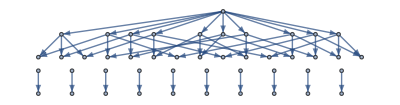

```mathematica
Graph[Map[InverseReal[#[[1]]]->InverseReal[#[[2]]]&,Select[AndToTable[ineqsnullSimp],With[{v=DeleteDuplicates[ListofVars[#]]},Length[#[[1]]]+Length[#[[2]]]==0]&]],GraphLayout->"LayeredDigraphEmbedding"]
```

```mathematica
Graph[Map[InverseReal[#[[1]]]->InverseReal[#[[2]]]&,Select[AndToTable[ineqsnullSimpreal],With[{v=DeleteDuplicates[ListofVars[#]]},Length[#[[1]]]+Length[#[[2]]]==0]&]],GraphLayout->"LayeredDigraphEmbedding"]//VertexCount
```

52

```mathematica
Graph[
Join[
Map[InverseReal[#[[1]]]->InverseReal[#[[2]]]&,Select[AndToTable[ineqsnullSimpreal],With[{v=DeleteDuplicates[ListofVars[#]]},Length[#[[1]]]+Length[#[[2]]]==0]&]],
Map[InverseReal[#[[1]]]->InverseReal[#[[2]]]&,Select[AndToTable[ineqsnullSimp],With[{v=DeleteDuplicates[ListofVars[#]]},Length[#[[1]]]+Length[#[[2]]]==0]&]]
],GraphLayout->"LayeredDigraphEmbedding"]//VertexCount
```

98

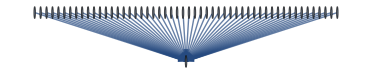

```mathematica
Graph[Map[InverseReal[#[[1]]]->InverseReal[#[[2]]]&,Select[AndToTable[ineqs],With[{v=DeleteDuplicates[ListofVars[#]]},Length[#[[1]]]+Length[#[[2]]]==0]&]],GraphLayout->"LayeredDigraphEmbedding"]
```

```mathematica
Select[ineqsnullSimp,Length[ListofVars[#]]==2&]
```

```mathematica
n14x2x35≥n1345x2
```